```mathematica
(* WALKING KINEMATICS: STICK FIGURE PLUS PELVIC VECTOR ANGLE ANALYSIS - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires input of single trial at a time and the data outputs from WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb *)
(*TrialMatrix information
KM01_RUN_02 [1,1]
KM02_RUN_01[2,1], KM02_RUN_02[2,2], KM02_RUN_09[2,3]
KM04_RUN_09[3,1], KM04_RUN_11[3,2], KM04_RUN_12[3,3]
KM05_RUN_04[4,1], KM05_RUN_08[4,2]
KM06_RUN_11[5,1], KM06_RUN_12[5,2], KM06_RUN_13[5,3], KM06_RUN_15[5,4], KM06_RUN_16[5,5]
KM07_RUN_14[6,1], KM07_RUN_16[6,2], KM07_RUN_17[6,3]
KM08_RUN_09[7,1], KM08_RUN_10[7,2]
KM23_RUN_01[8,1], KM23_RUN_02[8,2], KM23_RUN_03[8,3], KM23_RUN_05[8,4]*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

dataDirectory="YOUR DIRECTORY TO ARCHIVED .DAT DATA"; 
(*Set the directory where archived data from the "Code to Archive Data" notebook was exported to*)

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(***********************************************************************************)

(* Determine animal filename *)

Needs["GraphUtilities`"]
whatFrog[filename_]:=StringTake[filename,{3,4}](*extracts the animal number*)
trialFiles=FileNames[];
ntrials=Length[trialFiles];
trialMatrix=GatherBy[trialFiles,whatFrog];(*organize the trials in a matrix *)
ExpressionTreePlot[trialMatrix,VertexLabeling->Tooltip];

(******************************************************************************************)

(*INPUT - Type Animal Filename *)

animalfilename=trialMatrix[[4,1]] (*Change this to match trial matrix information above*)
(*e.g. animalfilename=trailMatrix[[8,4]] uses KM23_RUN_05*)

(******************************************************************************************)

(* Import raw data *)

allrawtrialdata=Import[animalfilename,"Data"];

(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

filenamerow=Flatten[Position[metadata,animalfilename]][[1]];

SVL=metadata[[filenamerow,2]];
Framerate=metadata[[filenamerow,3]];
TotalNumberRawFramesDigitised=metadata[[filenamerow,4]];
FirstFrame=metadata[[filenamerow,6]];
FinalFrame=metadata[[filenamerow,7]];
EndofFrames=metadata[[filenamerow,8]]; (*Total number of frames from first to final*)
StartofStance=metadata[[filenamerow,9]];
StartofSwing=metadata[[filenamerow,10]];
StartofLimbCycle=metadata[[filenamerow,11]];
EndofLimbCycle=metadata[[filenamerow,12]];
SingleStrideFrameCount=metadata[[filenamerow,13]];
SingleStrideTimeDuration=metadata[[filenamerow,14]];
AnimalDataTrialforexporting=metadata[[filenamerow,16]];

(***********************************************************************************)

(* Load filtering package/info *)

Needs["Biomechanics`"]; (*"Biomechanics" notebook provided*)

Duration=EndofFrames/Framerate;
DT=1/Framerate;(*sample interval, s*)
FC=30 ;(*cutoff frequency*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Partition raw data for filtering*)

nonfilteredend=Dimensions[allrawtrialdata][[1]];
allrawLMdata=Table[
fullframe=allrawtrialdata[[i]];
Partition[fullframe,3]
,{i,1,nonfilteredend}];

allrawLMdataX=Table[allrawLMdata[[All,i,1]],{i,1,12}];
allrawLMdataY=Table[allrawLMdata[[All,i,2]],{i,1,12}];
allrawLMdataZ=Table[allrawLMdata[[All,i,3]],{i,1,12}];

(*****************************************************************************************)

(* Apply filter to raw XYZ data *)

allLMdataX=Table[BFilterR[allrawLMdataX[[i,All]],FC,DT],{i,1,12}];
allLMdataY=Table[BFilterR[allrawLMdataY[[i,All]],FC,DT],{i,1,12}];
allLMdataZ=Table[BFilterR[allrawLMdataZ[[i,All]],FC,DT],{i,1,12}];
```

```mathematica
(*****************************************************************************************)

(* Re-join filtered data *)

end=Length[allLMdataX[[1]]];
allLMdata =Transpose[Table[Join[{allLMdataX[[i,f]]},{allLMdataY[[i,f]]},{allLMdataZ[[i,f]]}],{i,1,12},{f,1,end}]];

Dimensions[allLMdata];

(******************************************************************************************)

(* Partition per marker to build stick figure *)

LM1allframes=allLMdata[[All,1,All]];
LM2allframes=allLMdata[[All,2,All]];
LM3allframes=allLMdata[[All,3,All]];
LM4allframes=allLMdata[[All,4,All]];
LM5allframes=allLMdata[[All,5,All]];
LM6allframes=allLMdata[[All,6,All]];
LM7allframes=allLMdata[[All,7,All]];
LM8allframes=allLMdata[[All,8,All]];
LM9allframes=allLMdata[[All,9,All]];
LM10allframes=allLMdata[[All,10,All]];
LM11allframes=allLMdata[[All,11,All]];
LM12allframes=allLMdata[[All,12,All]];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Build stick figure *)

(* Build each element of stick figure *)
(* 1. Body triangles *)

BodyTriangle1LMJoin=Table[Join[LM5allframes[[f]],LM6allframes[[f]],LM7allframes[[f]],LM5allframes[[f]]],{f,1,end}];
BodyTriangle1=Table[singleframe=BodyTriangle1LMJoin[[f]];Partition[singleframe,3],{f,1,end}];


BodyTriangle2LMJoin=Table[Join[LM8allframes[[f]],LM9allframes[[f]],LM10allframes[[f]],LM8allframes[[f]]],{f,1,end}];
BodyTriangle2=Table[singleframe=BodyTriangle2LMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(* 2. Leg *)

LegLMJoin=Table[Join[LM1allframes[[f]],LM2allframes[[f]],LM3allframes[[f]],LM4allframes[[f]]],{f,1,end}];
Leg=Table[singleframe=LegLMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(* 3. Midline *)

MidlineLMJoin=Table[Join[LM10allframes[[f]],LM11allframes[[f]],LM12allframes[[f]],LM5allframes[[f]]],{f,1,end}];
Midline=Table[singleframe=MidlineLMJoin[[f]];Partition[singleframe,3],{f,1,end}];

(***************************************************************************)

(* Plot the figure *)

Manipulate[
singleframeBT1=BodyTriangle1[[frame]];
BT1graph1=Graphics3D[Line[singleframeBT1]];
BT1graph2=ListPointPlot3D[singleframeBT1,PlotStyle->Red];
BT1plot=Show[BT1graph1,BT1graph2];

singleframeBT2=BodyTriangle2[[frame]];
BT2graph1=Graphics3D[Line[singleframeBT2]];
BT2graph2=ListPointPlot3D[singleframeBT2,PlotStyle->Red];
BT2plot=Show[BT2graph1,BT2graph2];

singleframeLeg=Leg[[frame]];
Lgraph1=Graphics3D[Line[singleframeLeg]];
Lgraph2=ListPointPlot3D[singleframeLeg,PlotStyle->Red];
Legplot=Show[Lgraph1,Lgraph2];

singleframeMidLine=Midline[[frame]];
MidLinegraph1=Graphics3D[Line[singleframeMidLine]];
MidLinegraph2=ListPointPlot3D[singleframeMidLine,PlotStyle->Red];
MidLineplot=Show[MidLinegraph1,MidLinegraph2];

FrogStickFigure=Show[BT1plot,BT2plot,Legplot,MidLineplot,PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]

,{frame,1,end,1}]; (*remove this semicolon to view 3D stick figure*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Mathematically tether the frog *)

(*1. chunk out frames I want - the good frames of calibrated steady forward locmotion(first frame-final frame) - from this point onwards to analyse all data it'll be 1 to end of frames*)

chunkedallLMdata=allLMdata[[IntegerPart[FirstFrame];;IntegerPart[FinalFrame]]];
Dimensions[chunkedallLMdata];


(*2. tether the frog at the hip LM *)

VentTetheredLMs=Table[
CurrentLMs=chunkedallLMdata[[frame]];
Origin={0,0,0};
VentDifference=CurrentLMs[[5]]-Origin;
TetheredLMs=Table[CurrentLMs[[i]]-VentDifference,{i,1,12}]
,{frame,1,EndofFrames}];

(* 3. create new tethered LMs *)
(* {frames,xyz} *)

LM1allframesTV=VentTetheredLMs[[All,1,All]];
LM2allframesTV=VentTetheredLMs[[All,2,All]];
LM3allframesTV=VentTetheredLMs[[All,3,All]];
LM4allframesTV=VentTetheredLMs[[All,4,All]];
LM5allframesTV=VentTetheredLMs[[All,5,All]];
LM6allframesTV=VentTetheredLMs[[All,6,All]];
LM7allframesTV=VentTetheredLMs[[All,7,All]];
LM8allframesTV=VentTetheredLMs[[All,8,All]];
LM9allframesTV=VentTetheredLMs[[All,9,All]];
LM10allframesTV=VentTetheredLMs[[All,10,All]];
LM11allframesTV=VentTetheredLMs[[All,11,All]];
LM12allframesTV=VentTetheredLMs[[All,12,All]];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Build tethered stick figure *)

(* Build each element of tethered stick figure *)

(* 1. Body triangles *)

BodyTriangle1LMJoinTV=Table[Join[LM5allframesTV[[f]],LM6allframesTV[[f]],LM7allframesTV[[f]],LM5allframesTV[[f]]],{f,1,EndofFrames}];
BodyTriangle1TV=Table[singleframe=BodyTriangle1LMJoinTV[[f]];Partition[singleframe,3],{f,1,EndofFrames}];


BodyTriangle2LMJoinTV=Table[Join[LM8allframesTV[[f]],LM9allframesTV[[f]],LM10allframesTV[[f]],LM8allframesTV[[f]]],{f,1,EndofFrames}];
BodyTriangle2TV=Table[singleframe=BodyTriangle2LMJoinTV[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 2. Leg *)

LegLMJoinTV=Table[Join[LM1allframesTV[[f]],LM2allframesTV[[f]],LM3allframesTV[[f]],LM4allframesTV[[f]]],{f,1,EndofFrames}];
LegTV=Table[singleframe=LegLMJoinTV[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 3. Midline *)

MidlineLMJoinTV=Table[Join[LM10allframesTV[[f]],LM11allframesTV[[f]],LM12allframesTV[[f]],LM5allframesTV[[f]]],{f,1,EndofFrames}];
MidlineTV=Table[singleframe=MidlineLMJoinTV[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 4. Hiplines *)

HipLinesraw=Table[
LM4singleframeTV=LM4allframesTV[[i]];
xyoffset={10,0,0};
HipLinexy=LM4singleframeTV+xyoffset;
yzoffset={0,0,10};
HipLineyz=LM4singleframeTV+yzoffset;
AllHipLinesJoined=Join[HipLinexy,LM4singleframeTV,HipLineyz]
,{i,1,EndofFrames}];

HipLines=Table[
HipLinessingleframe=HipLinesraw[[i]];
Partition[HipLinessingleframe,3]
,{i,1,EndofFrames}];

(***************************************************************************)

(* Plot the figure *)

Manipulate[
singleframeBT1TV=BodyTriangle1TV[[frame]];
BT1graph1TV=Graphics3D[Line[singleframeBT1TV]];
BT1graph2TV=ListPointPlot3D[singleframeBT1TV,PlotStyle->Red];
BT1plotTV=Show[BT1graph1TV,BT1graph2TV];

singleframeBT2TV=BodyTriangle2TV[[frame]];
BT2graph1TV=Graphics3D[Line[singleframeBT2TV]];
BT2graph2TV=ListPointPlot3D[singleframeBT2TV,PlotStyle->Red];
BT2plotTV=Show[BT2graph1TV,BT2graph2TV];

singleframeLegTV=LegTV[[frame]];
Lgraph1TV=Graphics3D[Line[singleframeLegTV]];
Lgraph2TV=ListPointPlot3D[singleframeLegTV,PlotStyle->Red];
LegplotTV=Show[Lgraph1TV,Lgraph2TV];

singleframeMidLineTV=MidlineTV[[frame]];
MidLinegraph1TV=Graphics3D[Line[singleframeMidLineTV]];
MidLinegraph2TV=ListPointPlot3D[singleframeMidLineTV,PlotStyle->Red];
MidLineplotTV=Show[MidLinegraph1TV,MidLinegraph2TV];


(*SingleframeHiplinesplot=HipLines[[frame]];
Hiplinesplot1=Graphics3D[Line[singleframeHiplinesplot]];
Hiplinesplot2=ListPointPlot3D[singleframeHiplinesplot,PlotStyle->Green];
Hiplineforstickfigure=Show[Hiplinesplot1,Hiplinesplot2];*)


FrogStickFigureTV=Show[BT1plotTV,BT2plotTV,LegplotTV,MidLineplotTV,(*Hiplineforstickfigure,*)PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]
,{frame,1,EndofFrames,1}]; (*remove this semicolon to view 3D stick figure tethered at the hip*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Correcting for whole body axis angle - Model 1*)

(*body angle*)
(*first find the change in body angle throughout time*)
(*only do x,y components and add if statement to say if the y co-ordinate of the bodyaxis vector is negative rotate by positve angle by if it is positive rotate by negative angle*)

BodyAxisAngle=Table[
BodyAxisLine=LM10allframesTV[[f,{1,2}]]-LM5allframesTV[[f,{1,2}]];
StraightLinefromVentinX=LM5allframesTV[[f,{1,2}]]+{10,0};
If[BodyAxisLine[[2]]<0,BAAngle=VectorAngle[BodyAxisLine,StraightLinefromVentinX],BAAngle=-VectorAngle[BodyAxisLine,StraightLinefromVentinX]];
BAAngle
,{f,1,EndofFrames}];

(*Then make rotation matrix for each of the body axis angles*)

BodyAxisCorrection=Table[
RotationMatrix[BodyAxisAngle[[f]],{0,0,1}]
,{f,1,EndofFrames}];


(*apply the rotation matrix*)

BACorrectedLMs=Table[
BARotationraw=BodyAxisCorrection[[f]].(Transpose[VentTetheredLMs[[f]]]);
BARotatedTransposedLMs=Transpose[BARotationraw]
,{f,1,EndofFrames}];

(*************************************************************************************)

(*Make new body axis corrected LMs *)

BACLM1allframes=BACorrectedLMs[[All,1,All]];
BACLM2allframes=BACorrectedLMs[[All,2,All]];
BACLM3allframes=BACorrectedLMs[[All,3,All]];
BACLM4allframes=BACorrectedLMs[[All,4,All]];
BACLM5allframes=BACorrectedLMs[[All,5,All]];
BACLM6allframes=BACorrectedLMs[[All,6,All]];
BACLM7allframes=BACorrectedLMs[[All,7,All]];
BACLM8allframes=BACorrectedLMs[[All,8,All]];
BACLM9allframes=BACorrectedLMs[[All,9,All]];
BACLM10allframes=BACorrectedLMs[[All,10,All]];
BACLM11allframes=BACorrectedLMs[[All,11,All]];
BACLM12allframes=BACorrectedLMs[[All,12,All]];

(*************************************************************************************)

(*Make new body axis correct frog stick figure *)

BACBodyTriangle1LMJoin=Table[Join[BACLM5allframes[[f]],BACLM6allframes[[f]],BACLM7allframes[[f]],BACLM5allframes[[f]]],{f,1,EndofFrames}];
BACBodyTriangle1=Table[singleframe=BACBodyTriangle1LMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];


BACBodyTriangle2LMJoin=Table[Join[BACLM8allframes[[f]],BACLM9allframes[[f]],BACLM10allframes[[f]],BACLM8allframes[[f]]],{f,1,EndofFrames}];
BACBodyTriangle2=Table[singleframe=BACBodyTriangle2LMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 2. Leg *)

BACLegLMJoin=Table[Join[BACLM1allframes[[f]],BACLM2allframes[[f]],BACLM3allframes[[f]],BACLM4allframes[[f]]],{f,1,EndofFrames}];
BACLeg=Table[singleframe=BACLegLMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 3. Midline *)

BACMidlineLMJoin=Table[Join[BACLM10allframes[[f]],BACLM11allframes[[f]],BACLM12allframes[[f]],BACLM5allframes[[f]]],{f,1,EndofFrames}];
BACMidline=Table[singleframe=BACMidlineLMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(*************************************************************************************)

(*Plot body axis corrected (BAC) dynamic stick figure*)

Manipulate[
singleframeBACBT1=BACBodyTriangle1[[frame]];
BACBT1graph1=Graphics3D[Line[singleframeBACBT1]];
BACBT1graph2=ListPointPlot3D[singleframeBACBT1,PlotStyle->Red];
BACBT1plot=Show[BACBT1graph1,BACBT1graph2];

singleframeBACBT2=BACBodyTriangle2[[frame]];
BACBT2graph1=Graphics3D[Line[singleframeBACBT2]];
BACBT2graph2=ListPointPlot3D[singleframeBACBT2,PlotStyle->Red];
BACBT2plot=Show[BACBT2graph1,BACBT2graph2];

singleframeBACLeg=BACLeg[[frame]];
BACLgraph1=Graphics3D[Line[singleframeBACLeg]];
BACLgraph2=ListPointPlot3D[singleframeBACLeg,PlotStyle->Red];
BACLegplot=Show[BACLgraph1,BACLgraph2];

singleframeBACMidLine=BACMidline[[frame]];
BACMidLinegraph1=Graphics3D[Line[singleframeBACMidLine]];
BACMidLinegraph2=ListPointPlot3D[singleframeBACMidLine,PlotStyle->Red];
BACMidLineplot=Show[BACMidLinegraph1,BACMidLinegraph2];

RedStraightLineinX=Graphics3D[{Red,Line[{LM5allframesTV[[frame]]-{50,0,0},LM5allframesTV[[frame]]+{50,0,0}}]}];

BACFrogStickFigure=Show[BACBT1plot,BACBT2plot,BACLegplot,BACMidLineplot,RedStraightLineinX,PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]

,{frame,1,EndofFrames,1}];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Now correct for pelvic angle after body axis rotation - Model 2*)

(*pelvic angle*)
(*first find the change in pelvic angle throughout time*)
(*only do x,y components and add if statement to say if the y co-ordinate of the bodyaxis vector is negative rotate by positve angle by if it is positive rotate by negative angle*)

PelvicAngle=Table[
PelvisLine=BACLM12allframes[[f,{1,2}]]-BACLM5allframes[[f,{1,2}]];
StraightLinefromVentinX=LM5allframesTV[[f,{1,2}]]+{10,0};
If[PelvisLine[[2]]<0,PAngle=VectorAngle[PelvisLine,StraightLinefromVentinX],PAngle=-VectorAngle[PelvisLine,StraightLinefromVentinX]];
PAngle
,{f,1,EndofFrames}];

(*Then make rotation matrix for each of the body axis angles*)

PelvicAngleCorrection=Table[
RotationMatrix[PelvicAngle[[f]],{0,0,1}]
,{f,1,EndofFrames}];


(*apply the rotation matrix*)

PandBACorrectedLMs=Table[
PRotationraw=PelvicAngleCorrection[[f]].(Transpose[BACorrectedLMs[[f]]]);
PRotatedTransposedBACLMs=Transpose[PRotationraw]
,{f,1,EndofFrames}];

(*************************************************************************************)

(*Make pelvic vector and body axis corrected LMs *)

PandBACLM1allframes=PandBACorrectedLMs[[All,1,All]];
PandBACLM2allframes=PandBACorrectedLMs[[All,2,All]];
PandBACLM3allframes=PandBACorrectedLMs[[All,3,All]];
PandBACLM4allframes=PandBACorrectedLMs[[All,4,All]];
PandBACLM5allframes=PandBACorrectedLMs[[All,5,All]];
PandBACLM6allframes=PandBACorrectedLMs[[All,6,All]];
PandBACLM7allframes=PandBACorrectedLMs[[All,7,All]];
PandBACLM8allframes=PandBACorrectedLMs[[All,8,All]];
PandBACLM9allframes=PandBACorrectedLMs[[All,9,All]];
PandBACLM10allframes=PandBACorrectedLMs[[All,10,All]];
PandBACLM11allframes=PandBACorrectedLMs[[All,11,All]];
PandBACLM12allframes=PandBACorrectedLMs[[All,12,All]];

(*************************************************************************************)

(*Make pelvic vector and body axis correct frog stick figure *)

PandBACBodyTriangle1LMJoin=Table[Join[PandBACLM5allframes[[f]],PandBACLM6allframes[[f]],PandBACLM7allframes[[f]],PandBACLM5allframes[[f]]],{f,1,EndofFrames}];
PandBACBodyTriangle1=Table[singleframe=PandBACBodyTriangle1LMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];


PandBACBodyTriangle2LMJoin=Table[Join[PandBACLM8allframes[[f]],PandBACLM9allframes[[f]],PandBACLM10allframes[[f]],PandBACLM8allframes[[f]]],{f,1,EndofFrames}];
PandBACBodyTriangle2=Table[singleframe=PandBACBodyTriangle2LMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 2. Leg *)

PandBACLegLMJoin=Table[Join[PandBACLM1allframes[[f]],PandBACLM2allframes[[f]],PandBACLM3allframes[[f]],PandBACLM4allframes[[f]]],{f,1,EndofFrames}];
PandBACLeg=Table[singleframe=PandBACLegLMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(* 3. Midline *)

PandBACMidlineLMJoin=Table[Join[PandBACLM10allframes[[f]],PandBACLM11allframes[[f]],PandBACLM12allframes[[f]],PandBACLM5allframes[[f]]],{f,1,EndofFrames}];
PandBACMidline=Table[singleframe=PandBACMidlineLMJoin[[f]];Partition[singleframe,3],{f,1,EndofFrames}];

(*************************************************************************************)

(*Plot Pelvic vector and body axis corrected (PandBAC) dynamic stick figure*)

Manipulate[
singleframePandBACBT1=PandBACBodyTriangle1[[frame]];
PandBACBT1graph1=Graphics3D[Line[singleframePandBACBT1]];
PandBACBT1graph2=ListPointPlot3D[singleframePandBACBT1,PlotStyle->Red];
PandBACBT1plot=Show[PandBACBT1graph1,PandBACBT1graph2];

singleframePandBACBT2=PandBACBodyTriangle2[[frame]];
PandBACBT2graph1=Graphics3D[Line[singleframePandBACBT2]];
PandBACBT2graph2=ListPointPlot3D[singleframePandBACBT2,PlotStyle->Red];
PandBACBT2plot=Show[PandBACBT2graph1,PandBACBT2graph2];

singleframePandBACLeg=PandBACLeg[[frame]];
PandBACLgraph1=Graphics3D[Line[singleframePandBACLeg]];
PandBACLgraph2=ListPointPlot3D[singleframePandBACLeg,PlotStyle->Red];
PandBACLegplot=Show[PandBACLgraph1,PandBACLgraph2];

singleframePandBACMidLine=PandBACMidline[[frame]];
PandBACMidLinegraph1=Graphics3D[Line[singleframePandBACMidLine]];
PandBACMidLinegraph2=ListPointPlot3D[singleframePandBACMidLine,PlotStyle->Red];
PandBACMidLineplot=Show[PandBACMidLinegraph1,PandBACMidLinegraph2];

RedStraightLineinX=Graphics3D[{Red,Line[{LM5allframesTV[[frame]]-{50,0,0},LM5allframesTV[[frame]]+{50,0,0}}]}];

PandBACFrogStickFigure=Show[PandBACBT1plot,PandBACBT2plot,PandBACLegplot,PandBACMidLineplot,RedStraightLineinX,PlotRange->{{-50,200},{-50,200},{-50,100}},AspectRatio->1]

,{frame,1,EndofFrames,1}];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(* Add in the joint motion trajectories with and without pelvic vector rotation i.e. from Models 1 and 2 - Both in same plot - ALL DATA *)


JointMotionTrajectoriesAllData=Manipulate[
range=75;

BACLegGraph1=Graphics3D[Line[BACLeg[[frame]]]];
BACLegGraph2=ListPointPlot3D[BACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
BACLegGraph=Show[BACLegGraph2,BACLegGraph1];

BACBodyTriangle1Graph1=Graphics3D[Line[BACBodyTriangle1[[frame]]]];
BACBodyTriangle1Graph2=ListPointPlot3D[BACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle1Graph=Show[BACBodyTriangle1Graph2,BACBodyTriangle1Graph1];

BACBodyTriangle2Graph1=Graphics3D[Line[BACBodyTriangle2[[frame]]]];
BACBodyTriangle2Graph2=ListPointPlot3D[BACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle2Graph=Show[BACBodyTriangle2Graph2,BACBodyTriangle2Graph1];

BACMidlineGraph1=Graphics3D[Line[BACMidline[[frame]]]];
BACMidlineGraph2=ListPointPlot3D[BACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACMidlineGraph=Show[BACMidlineGraph2,BACMidlineGraph1];

BACFrogStickFigurePlot=Show[BACLegGraph,BACBodyTriangle1Graph,BACBodyTriangle2Graph,BACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

BACFrog=Show[BACFrogStickFigurePlot,GreenStraightLinefromVentinX,ImageSize->500];

TMTMotionWithPelvicRotation=ListPointPlot3D[BACLM1allframes[[1;;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithPelvicRotation=ListPointPlot3D[BACLM2allframes[[1;;frame]],PlotStyle->Setting[1.]];
KneeMotionWithPelvicRotation=ListPointPlot3D[BACLM3allframes[[1;;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithPelvicRotation=Show[TMTMotionWithPelvicRotation,AnkleMotionWithPelvicRotation,KneeMotionWithPelvicRotation];

JointMotionsWithPelvicRotationStickFigure=Show[BACFrog,JointMotionsWithPelvicRotation,AxesLabel->{"x","y","z"},PlotLabel->"Joint motions with pelvic rotation"];

PandBACLegGraph1=Graphics3D[Line[PandBACLeg[[frame]]]];
PandBACLegGraph2=ListPointPlot3D[PandBACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
PandBACLegGraph=Show[PandBACLegGraph2,PandBACLegGraph1];

PandBACBodyTriangle1Graph1=Graphics3D[Line[PandBACBodyTriangle1[[frame]]]];
PandBACBodyTriangle1Graph2=ListPointPlot3D[PandBACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle1Graph=Show[PandBACBodyTriangle1Graph2,PandBACBodyTriangle1Graph1];

PandBACBodyTriangle2Graph1=Graphics3D[Line[PandBACBodyTriangle2[[frame]]]];
PandBACBodyTriangle2Graph2=ListPointPlot3D[PandBACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle2Graph=Show[PandBACBodyTriangle2Graph2,PandBACBodyTriangle2Graph1];

PandBACMidlineGraph1=Graphics3D[Line[PandBACMidline[[frame]]]];
PandBACMidlineGraph2=ListPointPlot3D[PandBACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACMidlineGraph=Show[PandBACMidlineGraph2,PandBACMidlineGraph1];

PandBACFrogStickFigurePlot=Show[PandBACLegGraph,PandBACBodyTriangle1Graph,PandBACBodyTriangle2Graph,PandBACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

PandBACFrog=Show[PandBACFrogStickFigurePlot,GreenStraightLinefromVentinX,ImageSize->500];

TMTMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM1allframes[[1;;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM2allframes[[1;;frame]],PlotStyle->Setting[1.]];
KneeMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM3allframes[[1;;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithNOPelvicRotation=Show[TMTMotionWithNOPelvicRotation,AnkleMotionWithNOPelvicRotation,KneeMotionWithNOPelvicRotation];

JointMotionsWithNOPelvicRotationStickFigure=Show[PandBACFrog,JointMotionsWithNOPelvicRotation,AxesLabel->{"x","y","z"},PlotLabel->"Joint motions without pelvic rotation"];


GraphicsRow[{JointMotionsWithPelvicRotationStickFigure,JointMotionsWithNOPelvicRotationStickFigure}]

,{frame,1,EndofFrames,1}];
```

```mathematica
(*****************************************************************************************)

(* Add in the joint motion trajectories with and without pelvic vector rotation i.e. from Models 1 and 2 - Both in same plot - SINGLE LIMB CYCLE *)

JointMotionTrajectoriesOneLimbCycle=Manipulate[
range=75;

BACLegGraph1=Graphics3D[Line[BACLeg[[frame]]]];
BACLegGraph2=ListPointPlot3D[BACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
BACLegGraph=Show[BACLegGraph2,BACLegGraph1];

BACBodyTriangle1Graph1=Graphics3D[Line[BACBodyTriangle1[[frame]]]];
BACBodyTriangle1Graph2=ListPointPlot3D[BACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle1Graph=Show[BACBodyTriangle1Graph2,BACBodyTriangle1Graph1];

BACBodyTriangle2Graph1=Graphics3D[Line[BACBodyTriangle2[[frame]]]];
BACBodyTriangle2Graph2=ListPointPlot3D[BACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle2Graph=Show[BACBodyTriangle2Graph2,BACBodyTriangle2Graph1];

BACMidlineGraph1=Graphics3D[Line[BACMidline[[frame]]]];
BACMidlineGraph2=ListPointPlot3D[BACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACMidlineGraph=Show[BACMidlineGraph2,BACMidlineGraph1];

BACFrogStickFigurePlot=Show[BACLegGraph,BACBodyTriangle1Graph,BACBodyTriangle2Graph,BACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

BACFrog=Show[BACFrogStickFigurePlot,GreenStraightLinefromVentinX,ImageSize->500];

TMTMotionWithPelvicRotation=ListPointPlot3D[BACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithPelvicRotation=ListPointPlot3D[BACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithPelvicRotation=ListPointPlot3D[BACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithPelvicRotation=Show[TMTMotionWithPelvicRotation,AnkleMotionWithPelvicRotation,KneeMotionWithPelvicRotation];

JointMotionsWithPelvicRotationStickFigure=Show[BACFrog,JointMotionsWithPelvicRotation,AxesLabel->{"x","y","z"},PlotLabel->"Joint motions with pelvic rotation"];

PandBACLegGraph1=Graphics3D[Line[PandBACLeg[[frame]]]];
PandBACLegGraph2=ListPointPlot3D[PandBACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
PandBACLegGraph=Show[PandBACLegGraph2,PandBACLegGraph1];

PandBACBodyTriangle1Graph1=Graphics3D[Line[PandBACBodyTriangle1[[frame]]]];
PandBACBodyTriangle1Graph2=ListPointPlot3D[PandBACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle1Graph=Show[PandBACBodyTriangle1Graph2,PandBACBodyTriangle1Graph1];

PandBACBodyTriangle2Graph1=Graphics3D[Line[PandBACBodyTriangle2[[frame]]]];
PandBACBodyTriangle2Graph2=ListPointPlot3D[PandBACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle2Graph=Show[PandBACBodyTriangle2Graph2,PandBACBodyTriangle2Graph1];

PandBACMidlineGraph1=Graphics3D[Line[PandBACMidline[[frame]]]];
PandBACMidlineGraph2=ListPointPlot3D[PandBACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACMidlineGraph=Show[PandBACMidlineGraph2,PandBACMidlineGraph1];

PandBACFrogStickFigurePlot=Show[PandBACLegGraph,PandBACBodyTriangle1Graph,PandBACBodyTriangle2Graph,PandBACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

PandBACFrog=Show[PandBACFrogStickFigurePlot,GreenStraightLinefromVentinX,ImageSize->500];

TMTMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithNOPelvicRotation=Show[TMTMotionWithNOPelvicRotation,AnkleMotionWithNOPelvicRotation,KneeMotionWithNOPelvicRotation];

JointMotionsWithNOPelvicRotationStickFigure=Show[PandBACFrog,JointMotionsWithNOPelvicRotation,AxesLabel->{"x","y","z"},PlotLabel->"Joint motions without pelvic rotation"];


GraphicsRow[{JointMotionsWithPelvicRotationStickFigure,JointMotionsWithNOPelvicRotationStickFigure}]

,{frame,IntegerPart[StartofLimbCycle],IntegerPart[EndofLimbCycle],1}];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Pelvic vector angle data*)

Degrees=360./(2Pi);

PelvicAngleAllData=PelvicAngle*Degrees;

(**************************************************************)

(*Plot pelvic vector angle data*)

(*Plot settings and data*)

XValues=Table[x/Framerate,{x,1,EndofFrames}];

PelvicAngleDatatoPlot=Thread[{XValues,PelvicAngleAllData}];

PelvicAngleAxesStyle={AxesLabel->{"Time (s)","Pelvic angle (deg.)"},Ticks->All};
PelvicAngleGraphStyle={PlotRange->{{0,EndofFrames/250},{-14,16}},ImageSize->500};
PelvicLineStyle={Setting[0.],Thick};
DynamicPelvicLineStyle={Setting[0.7294117647058823],Thick};

StartStanceRange={{(N[StartofStance/Framerate]),-200},{(N[StartofStance/Framerate]),200}};
EndofLimbCycleRange={{(N[EndofLimbCycle/Framerate]),-200},{(N[EndofLimbCycle/Framerate]),200}};
StartSwingRange={{(N[StartofSwing/Framerate]),-200},{(N[StartofSwing/Framerate]),200}};
StancePhaseStyle=PlotStyle->{Black,Thick};
SwingPhaseStyle=PlotStyle->{Black,Thick,Dashed};
EndofLimbCycleStyle=PlotStyle->{Red,Thick};

PelvicAngleLegend=LineLegend[{{Black,Thick},{Black,Dashed},{Red,Thick}},{{"Start of stance phase"},{"Start of swing phase"},{"End of Limb cycle"}}];


StartofStanceLine=ListLinePlot[StartStanceRange,StancePhaseStyle];
EndofCycleLine=ListLinePlot[EndofLimbCycleRange,EndofLimbCycleStyle];
StartofSwingLine=ListLinePlot[StartSwingRange,SwingPhaseStyle];

(******************************************************************)

(*Static plot*)

PelvicAngleTimePlotnophaselines=ListLinePlot[PelvicAngleDatatoPlot,PelvicAngleAxesStyle,PelvicAngleGraphStyle,PlotStyle->PelvicLineStyle,PlotLegends->PelvicAngleLegend];
PelvicAngleTimePlot=Show[PelvicAngleTimePlotnophaselines,StartofStanceLine,EndofCycleLine,StartofSwingLine];

(*Dynamic plot*)

DynamicPelvicAnglenophaselines=Manipulate[ListLinePlot[PelvicAngleDatatoPlot[[1;;f]],PelvicAngleAxesStyle,PelvicAngleGraphStyle,PlotStyle->DynamicPelvicLineStyle,PlotLegends->PelvicAngleLegend],{f,1,EndofFrames,1}];
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

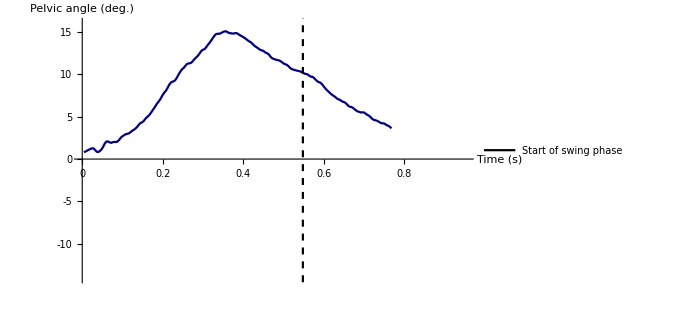

```mathematica
(*Crop Pelvic vector angle data to one hindlimb cycle*)

PelvicAngleData=PelvicAngleAllData[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];

(*Plot pelvic vector angle data - single limb cycle*)

(*Plot data*)

FramesinOneLimbCycle=EndofLimbCycle-StartofLimbCycle+1;

XValuesOneLimbCycle=Table[x/Framerate,{x,1,IntegerPart[FramesinOneLimbCycle]}];

PelvicAngleDatatoPlotOneLimbCyle=Thread[{XValuesOneLimbCycle,PelvicAngleData}];


(*Import relative start of swing phase*)

dataDirectory="Amber\\Data\\Kinematics Paper - Exported data\\Stride cycle event data";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];


StartofSwingOneLimbCycle=Flatten[Import[StringJoin[AnimalDataTrialforexporting,"_","Start of Swing relative frame number.xlsx"],"Data"]][[1]];


(*Plot settings*)

StartSwingRangeOneLimbCycle={{(N[StartofSwingOneLimbCycle/Framerate]),-200},{(N[StartofSwingOneLimbCycle/Framerate]),200}};

SwingPhaseStyleOneLimbCycle=PlotStyle->{Black,Thick,Dashed};

PelvicAngleLegendOneLimbCycle=LineLegend[{{Black,Dashed}},{{"Start of swing phase"}}];

StartofSwingLineOneLimbCycle=ListLinePlot[StartSwingRangeOneLimbCycle,SwingPhaseStyleOneLimbCycle];



(*Static plot*)

PelvicAngleTimePlotOneLimbCyclenophaselines=ListLinePlot[PelvicAngleDatatoPlotOneLimbCyle,PelvicAngleAxesStyle,PelvicAngleGraphStyle,PlotStyle->PelvicLineStyle,PlotLegends->PelvicAngleLegendOneLimbCycle];
PelvicAngleTimePlotOneLimbCycle=Show[PelvicAngleTimePlotOneLimbCyclenophaselines,StartofSwingLineOneLimbCycle]

(*Dynamic plot*)
DynamicPelvicAnglenophaselines=Manipulate[ListLinePlot[PelvicAngleDatatoPlotOneLimbCyle[[1;;f]],PelvicAngleAxesStyle,PelvicAngleGraphStyle,PlotStyle->DynamicPelvicLineStyle,PlotLegends->PelvicAngleLegendOneLimbCycle],{f,1,FramesinOneLimbCycle,1}]
```

```mathematica
(******************************************************************)

(*EXPORT DATA*)
(*Pelvic vector angle data - single limb cycle*)

dataDirectory="YOUR DITRECTORY FOR EXPORTED PELVIC VECTOR ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];


Export[StringJoin[AnimalDataTrialforexporting,"_","Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx"],PelvicAngleData];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Comparison analysis between fixed body axis model and fixed pevlic vector model*)

(*Find Maximum hip extension position in single limb cycle*)

dataDirectory="YOUR DIRECTORY FOR 3D JOINT ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*********************************************************************)

(*IMPORT 3D joint angle data*)

(*Hip*)
Hip=Import[StringJoin[AnimalDataTrialforexporting,"_","Hip 3D Joint Angle Data - One Limb Cycle - FILTERED.xlsx"],"Data"];

(*********************************************************************)

(*Finding frame of maximum hip extension between start stance and start of swing - NB Max hip extension will only refer to frame number within the limb cycle when start of stance becomes frame number 1 - ie the data is cropped. If data is not cropped, max hip extension can be found by adding 'StartofLimbCyle to MaxHipExtension*)

HipMAXANGLE=Max[Hip]

FrameofMAXANGLE=Position[Hip,HipMAXANGLE][[1,2]]
```

119.187

79

```mathematica
(******************************************************************************************)

(*EXPORT DATA*)

dataDirectory="YOUR DIRECTORY TO EXPORT MAXIMUM HIP EXTENSION DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","Maximum Hip Extension - One Limb Cycle.xlsx"],FrameofMAXANGLE];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(******************************************************************************************)
```

```mathematica
(*****************************************************************************************)

(* Add in the joint fore-aft excursion with and without pelvic vector rotation i.e. from Models 1 and 2 - Both in same plot - SINGLE LIMB CYCLE *)

JointMotionTrajectoriesForeAftEcursion=Manipulate[
range=75;

BACLegGraph1=Graphics3D[Line[BACLeg[[frame]]]];
BACLegGraph2=ListPointPlot3D[BACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
BACLegGraph=Show[BACLegGraph2,BACLegGraph1];

BACBodyTriangle1Graph1=Graphics3D[Line[BACBodyTriangle1[[frame]]]];
BACBodyTriangle1Graph2=ListPointPlot3D[BACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle1Graph=Show[BACBodyTriangle1Graph2,BACBodyTriangle1Graph1];

BACBodyTriangle2Graph1=Graphics3D[Line[BACBodyTriangle2[[frame]]]];
BACBodyTriangle2Graph2=ListPointPlot3D[BACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle2Graph=Show[BACBodyTriangle2Graph2,BACBodyTriangle2Graph1];

BACMidlineGraph1=Graphics3D[Line[BACMidline[[frame]]]];
BACMidlineGraph2=ListPointPlot3D[BACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACMidlineGraph=Show[BACMidlineGraph2,BACMidlineGraph1];

BACFrogStickFigurePlot=Show[BACLegGraph,BACBodyTriangle1Graph,BACBodyTriangle2Graph,BACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

BACFrog=Show[BACFrogStickFigurePlot,GreenStraightLinefromVentinX,ViewPoint->Top,ImageSize->300];



TMTMotionWithPelvicRotation=ListPointPlot3D[BACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithPelvicRotation=ListPointPlot3D[BACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithPelvicRotation=ListPointPlot3D[BACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithPelvicRotation=Show[TMTMotionWithPelvicRotation,AnkleMotionWithPelvicRotation,KneeMotionWithPelvicRotation];

JointMotionsWithPelvicRotationStickFigure=Show[BACFrog,JointMotionsWithPelvicRotation,AxesLabel->{"x","y"},Ticks->None,PlotLabel->"Fixed body axis model",LabelStyle->Directive[Bold,Black,FontFamily->"Calibri",FontSize->20],AxesStyle->Directive[Black,12]];







PandBACLegGraph1=Graphics3D[Line[PandBACLeg[[frame]]]];
PandBACLegGraph2=ListPointPlot3D[PandBACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
PandBACLegGraph=Show[PandBACLegGraph2,PandBACLegGraph1];

PandBACBodyTriangle1Graph1=Graphics3D[Line[PandBACBodyTriangle1[[frame]]]];
PandBACBodyTriangle1Graph2=ListPointPlot3D[PandBACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle1Graph=Show[PandBACBodyTriangle1Graph2,PandBACBodyTriangle1Graph1];

PandBACBodyTriangle2Graph1=Graphics3D[Line[PandBACBodyTriangle2[[frame]]]];
PandBACBodyTriangle2Graph2=ListPointPlot3D[PandBACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle2Graph=Show[PandBACBodyTriangle2Graph2,PandBACBodyTriangle2Graph1];

PandBACMidlineGraph1=Graphics3D[Line[PandBACMidline[[frame]]]];
PandBACMidlineGraph2=ListPointPlot3D[PandBACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACMidlineGraph=Show[PandBACMidlineGraph2,PandBACMidlineGraph1];

PandBACFrogStickFigurePlot=Show[PandBACLegGraph,PandBACBodyTriangle1Graph,PandBACBodyTriangle2Graph,PandBACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

PandBACFrog=Show[PandBACFrogStickFigurePlot,GreenStraightLinefromVentinX,ViewPoint->Top,ImageSize->300];



TMTMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithNOPelvicRotation=Show[TMTMotionWithNOPelvicRotation,AnkleMotionWithNOPelvicRotation,KneeMotionWithNOPelvicRotation];

JointMotionsWithNOPelvicRotationStickFigure=Show[PandBACFrog,JointMotionsWithNOPelvicRotation,AxesLabel->{"x","y"},Ticks->None,PlotLabel->"Fixed pelvic vector model",LabelStyle->Directive[Bold,Black,FontFamily->"Calibri",FontSize->20],AxesStyle->Directive[Black,12]];


GraphicsRow[{JointMotionsWithPelvicRotationStickFigure,JointMotionsWithNOPelvicRotationStickFigure}]

,{frame,IntegerPart[StartofLimbCycle],IntegerPart[FrameofMAXANGLE+StartofLimbCycle],1}];
```

```mathematica
JointMotionTrajectoriesForeAftEcursion=Table[
range=75;

BACLegGraph1=Graphics3D[Line[BACLeg[[frame]]]];
BACLegGraph2=ListPointPlot3D[BACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
BACLegGraph=Show[BACLegGraph2,BACLegGraph1];

BACBodyTriangle1Graph1=Graphics3D[Line[BACBodyTriangle1[[frame]]]];
BACBodyTriangle1Graph2=ListPointPlot3D[BACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle1Graph=Show[BACBodyTriangle1Graph2,BACBodyTriangle1Graph1];

BACBodyTriangle2Graph1=Graphics3D[Line[BACBodyTriangle2[[frame]]]];
BACBodyTriangle2Graph2=ListPointPlot3D[BACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACBodyTriangle2Graph=Show[BACBodyTriangle2Graph2,BACBodyTriangle2Graph1];

BACMidlineGraph1=Graphics3D[Line[BACMidline[[frame]]]];
BACMidlineGraph2=ListPointPlot3D[BACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
BACMidlineGraph=Show[BACMidlineGraph2,BACMidlineGraph1];

BACFrogStickFigurePlot=Show[BACLegGraph,BACBodyTriangle1Graph,BACBodyTriangle2Graph,BACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

BACFrog=Show[BACFrogStickFigurePlot,GreenStraightLinefromVentinX,ViewPoint->Top,ImageSize->300];



TMTMotionWithPelvicRotation=ListPointPlot3D[BACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithPelvicRotation=ListPointPlot3D[BACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithPelvicRotation=ListPointPlot3D[BACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithPelvicRotation=Show[TMTMotionWithPelvicRotation,AnkleMotionWithPelvicRotation,KneeMotionWithPelvicRotation];

JointMotionsWithPelvicRotationStickFigure=Show[BACFrog,JointMotionsWithPelvicRotation,AxesLabel->{"x","y"},Ticks->None,PlotLabel->"Fixed body axis model",LabelStyle->Directive[Bold,Black,FontFamily->"Calibri",FontSize->20],AxesStyle->Directive[Black,12]];







PandBACLegGraph1=Graphics3D[Line[PandBACLeg[[frame]]]];
PandBACLegGraph2=ListPointPlot3D[PandBACLeg[[frame]],PlotStyle->Setting[0.788235294117647],PlotRange->{{-range,range},{-range,range},{-range,range}},AspectRatio->1];
PandBACLegGraph=Show[PandBACLegGraph2,PandBACLegGraph1];

PandBACBodyTriangle1Graph1=Graphics3D[Line[PandBACBodyTriangle1[[frame]]]];
PandBACBodyTriangle1Graph2=ListPointPlot3D[PandBACBodyTriangle1[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle1Graph=Show[PandBACBodyTriangle1Graph2,PandBACBodyTriangle1Graph1];

PandBACBodyTriangle2Graph1=Graphics3D[Line[PandBACBodyTriangle2[[frame]]]];
PandBACBodyTriangle2Graph2=ListPointPlot3D[PandBACBodyTriangle2[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACBodyTriangle2Graph=Show[PandBACBodyTriangle2Graph2,PandBACBodyTriangle2Graph1];

PandBACMidlineGraph1=Graphics3D[Line[PandBACMidline[[frame]]]];
PandBACMidlineGraph2=ListPointPlot3D[PandBACMidline[[frame]],PlotStyle->Setting[0.788235294117647],AspectRatio->1];
PandBACMidlineGraph=Show[PandBACMidlineGraph2,PandBACMidlineGraph1];

PandBACFrogStickFigurePlot=Show[PandBACLegGraph,PandBACBodyTriangle1Graph,PandBACBodyTriangle2Graph,PandBACMidlineGraph];

GreenStraightLinefromVentinX=Graphics3D[{Setting[0.2627450980392157],Line[{LM5allframesTV[[1]]-{25,0,0},LM5allframesTV[[1]]+{50,0,0}}]}];

PandBACFrog=Show[PandBACFrogStickFigurePlot,GreenStraightLinefromVentinX,ViewPoint->Top,ImageSize->300];



TMTMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM1allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.5686274509803921]];
AnkleMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM2allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[1.]];
KneeMotionWithNOPelvicRotation=ListPointPlot3D[PandBACLM3allframes[[IntegerPart[StartofLimbCycle];;frame]],PlotStyle->Setting[0.011764705882352941]];

JointMotionsWithNOPelvicRotation=Show[TMTMotionWithNOPelvicRotation,AnkleMotionWithNOPelvicRotation,KneeMotionWithNOPelvicRotation];

JointMotionsWithNOPelvicRotationStickFigure=Show[PandBACFrog,JointMotionsWithNOPelvicRotation,AxesLabel->{"x","y"},Ticks->None,PlotLabel->"Fixed pelvic vector model",LabelStyle->Directive[Bold,Black,FontFamily->"Calibri",FontSize->20],AxesStyle->Directive[Black,12]];


GraphicsRow[{JointMotionsWithPelvicRotationStickFigure,JointMotionsWithNOPelvicRotationStickFigure}]

,{frame,IntegerPart[StartofLimbCycle],IntegerPart[FrameofMAXANGLE+StartofLimbCycle],1}];
```

```mathematica
excursioncomparisonpic=JointMotionTrajectoriesForeAftEcursion[[FrameofMAXANGLE+1]]
FrameofMAXANGLE
```

-Graphics-

79

63

```mathematica
(*Export*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export[StringJoin[AnimalDataTrialforexporting,"_","cranio-caudal joint excusions Model 1 & 2 comparison.svg"],excursioncomparisonpic];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(*************************************************************************************************************************)


(*Joint distances travelled*)
(*Hindlimb step length between start of stance and the frame of max hip extensions (maximum distance over which the hindlimb joints retract)*)

(*Import Maxhipextension data*)

dataDirectory="YOUR DIRECTORY FOR MAXIMUM HIP EXTENSION POSITION DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

MaxHipExtensiondata=Flatten[Import[StringJoin[AnimalDataTrialforexporting,"_","Maximum Hip Extension - One Limb Cycle.xlsx"],"Data"]];
MaxHipExtension=MaxHipExtensiondata[[1]];

(*Crop LM data to one limb cycle*)
BACLM1limbcycle=BACLM1allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];
PandBACLM1limbcycle=PandBACLM1allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];
BACLM2limbcycle=BACLM2allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];
PandBACLM2limbcycle=PandBACLM2allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];
BACLM3limbcycle=BACLM3allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];
PandBACLM3limbcycle=PandBACLM3allframes[[IntegerPart[StartofLimbCycle];;IntegerPart[EndofLimbCycle]]];

(*TMT joint distance travelled*)
TMTDistanceFixedBA=EuclideanDistance[BACLM1limbcycle[[1]],BACLM1limbcycle[[MaxHipExtension]]]
TMTDistanceFixedP=EuclideanDistance[PandBACLM1limbcycle[[1]],PandBACLM1limbcycle[[MaxHipExtension]]]
TMTHypotheticalGain=TMTDistanceFixedBA-TMTDistanceFixedP
```

39.766

32.8543

6.91174

```mathematica
(*Ankle joint distance travelled*)
AnkleDistanceFixedBA=EuclideanDistance[BACLM2limbcycle[[1]],BACLM2limbcycle[[MaxHipExtension]]]
AnkleDistanceFixedP=EuclideanDistance[PandBACLM2limbcycle[[1]],PandBACLM2limbcycle[[MaxHipExtension]]]
AnkleHypotheticalGain=AnkleDistanceFixedBA-AnkleDistanceFixedP
```

29.3437

23.7238

5.61998

```mathematica
18.94130445731375
```

18.9413

```mathematica
(*Knee joint distance travelled*)
KneeDistanceFixedBA=EuclideanDistance[BACLM3limbcycle[[1]],BACLM3limbcycle[[MaxHipExtension]]]
KneeDistanceFixedP=EuclideanDistance[PandBACLM3limbcycle[[1]],PandBACLM3limbcycle[[MaxHipExtension]]]
KneeHypotheticalGain=KneeDistanceFixedBA-KneeDistanceFixedP
```

29.2366

23.7341

5.50248

```mathematica
24.310964012630826
```

24.311

```mathematica
(******************************************************************************************)

(*EXPORT DATA - Joint distances travelled in both models and the hypothetical gain*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED JOINT DISTANCES TRAVELLED DATA7";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*TMT*)
Export[StringJoin[AnimalDataTrialforexporting,"_","TMT distance travelled - Model 1 Fixed body axis.xlsx"],TMTDistanceFixedBA];
Export[StringJoin[AnimalDataTrialforexporting,"_","TMT distance travelled - Model 2 Fixed pelvic vector.xlsx"],TMTDistanceFixedP];
Export[StringJoin[AnimalDataTrialforexporting,"_","TMT hypothetical gain in distance.xlsx"],TMTHypotheticalGain];

(*Ankle*)
Export[StringJoin[AnimalDataTrialforexporting,"_","Ankle distance travelled - Model 1 Fixed body axis.xlsx"],AnkleDistanceFixedBA];
Export[StringJoin[AnimalDataTrialforexporting,"_","Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx"],AnkleDistanceFixedP];
Export[StringJoin[AnimalDataTrialforexporting,"_","Ankle hypothetical gain in distance.xlsx"],AnkleHypotheticalGain];

(*Knee*)
Export[StringJoin[AnimalDataTrialforexporting,"_","Knee distance travelled - Model 1 Fixed body axis.xlsx"],KneeDistanceFixedBA];
Export[StringJoin[AnimalDataTrialforexporting,"_","Knee distance travelled - Model 2 Fixed pelvic vector.xlsx"],KneeDistanceFixedP];
Export[StringJoin[AnimalDataTrialforexporting,"_","Knee hypothetical gain in distance.xlsx"],KneeHypotheticalGain];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*Find maximum and minimum pelvic angles in the stride cycle*)

MaxPelvicAngle=Max[PelvicAngleData]

MinPelvicAngle=Min[PelvicAngleData]

(*Find total angluar excursion*)

PelvicAngluarExcursion=MaxPelvicAngle-MinPelvicAngle
```

15.0886

0.817497

14.2711

```mathematica
(******************************************************************************************)

(*EXPORT DATA*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED PELVIC VECTOR ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*Max*)
Export[StringJoin[AnimalDataTrialforexporting,"_","Max Pelvic Vector Angle - One Limb Cycle - FILTERED.xlsx"],MaxPelvicAngle];

(*Min*)
Export[StringJoin[AnimalDataTrialforexporting,"_","Min Pelvic Vector Angle - One Limb Cycle - FILTERED.xlsx"],MinPelvicAngle];

(*Total excursion*)
Export[StringJoin[AnimalDataTrialforexporting,"_","Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx"],PelvicAngluarExcursion];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```

```mathematica
(*end of code*)
```

```mathematica
(******************************************************************************************)
(******************************************************************************************)
```